```mathematica
dane=Import["/home/hodor/Desktop/numerki/dane.txt","Table"];
```

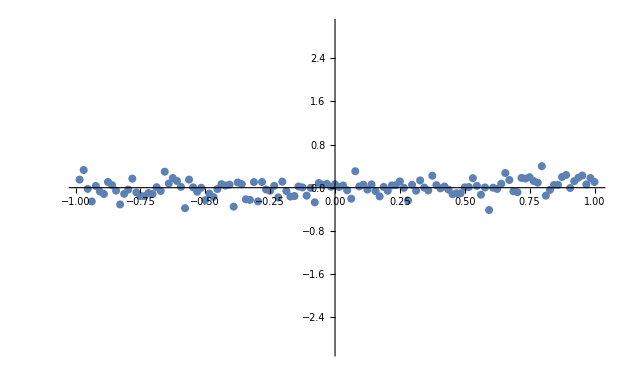

```mathematica
w=ListPlot[dane,PlotRange->{-3,3}]
```

```mathematica
X=dane[[All,1]];
```

```mathematica
Y=dane[[All,2]];
Ym={Y};
```

```mathematica
makepol[d_]:=
Module[{deegre=d},
At={ConstantArray[1,Length[X]]};
For[i=1,i<=deegre,i++,AppendTo[At,X^i]];
coef=LinearSolve[At.Transpose[At],At.Transpose[Ym]];
poly=(x^Range[0,deegre].coef)[[1]];
pol[p_]:=poly/.{x->p};
stdkw=Mean[(Y-Map[pol,X])^2];
Q=1/2*(pol[X]-Y).(pol[X]-Y)/stdkw;
Aic=Log[Q]+2*(deegre+1)/Length[X];
Cp=stdkw*Inverse[At.Transpose[At]];
{Aic,poly,Cp}
]
```

```mathematica
{v0,p0,c0}=makepol[0];
{v1,p1,c1}=makepol[1];
{v2,p2,c2}=makepol[2];
{v3,p3,c3}=makepol[3];
{v4,p4,c4}=makepol[4];
```

```mathematica
MatrixForm[c0]
MatrixForm[c1]
MatrixForm[c2]
MatrixForm[c3]
MatrixForm[c4]
```

(0.000163123)

(0.000151721 | -3.55552×10^-6
-3.55552×10^-6 | 0.000455107)

(0.000324099 | 5.06445×10^-6 | -0.000540208
5.06445×10^-6 | 0.000432562 | -0.0000253284
-0.000540208 | -0.0000253284 | 0.00162102)

(0.000324172 | -0.0000126604 | -0.000540792 | 0.0000295529
-0.0000126604 | 0.00270066 | 0.0000633174 | -0.003782
-0.000540792 | 0.0000633174 | 0.00162416 | -0.000147801
0.0000295529 | -0.003782 | -0.000147801 | 0.00630616)

(0.000501302 | 0.0000156682 | -0.00233989 | -0.0000365741 | 0.00210667
0.0000156682 | 0.00267824 | -0.000219489 | -0.00375472 | 0.000329435
-0.00233989 | -0.000219489 | 0.0196622 | 0.00051235 | -0.0210778
-0.0000365741 | -0.00375472 | 0.00051235 | 0.00626754 | -0.000768995
0.00210667 | 0.000329435 | -0.0210778 | -0.000768995 | 0.0246078)

```mathematica
Show[Plot[{p0,p1,p2,p3,p4},{x,-1,1},PlotLabels->{"d=0 AIC="<>ToString[v0],"d=1 AIC="<>ToString[v1],"d=2 AIC="<>ToString[v2],"d=3 AIC="<>ToString[v3],"d=4 AIC="<>ToString[v4]}],w,PlotRange->{-0.5,0.5}]
```

-Graphics-

0.00179656